```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Remove::rmnsm: There are no symbols matching ""<Global`*>"". ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/Remove/rmnsm",
ButtonNote->"Remove::rmnsm"]

```mathematica
SetDirectory["~/Desktop/Work/data/25nov16"]
```

/users/home/arway/Desktop/Work/data/25nov16

```mathematica
dat=Import["AllSpins.txt","Table"];
(*originGS=Import["gsorigin.dat","Table"];*)
actualGS=Import["ground_states.dat","Table"];
```

Import::nffil: File not found during Import.

```mathematica
mag1=Import["n1.000_.00001/fort.1","Table"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
mag=mag1[[All,2]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
Length[dat]
```

1364

```mathematica
nspins=(Length[dat])/4
spins=Table[{0,0,0},{i,1,nspins}];
```

341

```mathematica
Length[spins].17.11
```

341 .11 .17

```mathematica
Do[spins[[i,1]]=dat[[4i-2]];
spins[[i,2]]=dat[[4i-1]];
spins[[i,3]]=dat[[4i]],{i,1,nspins}]
```

Check (the last) spin configuration against the file.

```mathematica
spins[[1]]//MatrixForm
```

(-0.8414709847658229574 | -8.41471×10^-6 | 0.5403023058681397174
0.3789726836700167761 | 0.9254078587094114677 | -8.41471×10^-6
0.3789726836700167761 | 0.9254078587094114677 | -8.41471×10^-6)

Check the Byron relationship

```mathematica
tol=10^-6;
Do[Print["config",i-1," check a ",If[spins[[i,1,1]]+spins[[i,2,3]]<tol,0,"oops"], 
" check e ",
If[ spins[[i,2,2]]+spins[[i,3,1]]<tol,0,"oops"],
" check d ",
If[spins[[i,2,1]]+spins[[i,1,3]]+spins[[i,3,2]]<(tol),0,"oops"]],{i,1,1}]
```

config0 check a 0 check e oops check d oops

Now let’s take a look at what θ and ϕ values Andrew’s configurations correspond to.

tan ϕ = b/a (= sinθ sinϕ / sinθ cosϕ = y/x)
ArcTan[x,y]
cosθ=c

```mathematica
theta=Table[0,{i,1,nspins}];
phi=Table[0,{i,1,nspins}];
Do[theta[[i]]=ArcCos[spins[[i,1,3]]];
phi[[i]]=ArcTan[spins[[i,1,1]],spins[[i,1,2]]],{i,1,nspins}]
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

```mathematica
Bound[ϕ_]:=If[Cos[4 ϕ]==1,π/3,ArcSin[√((4-√(16-6(1-Cos[4 ϕ])))/(1-Cos[4ϕ]))]]
```

```mathematica
??Diamond
```

RowBox[{"Diamond", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "]"}] displays as RowBox[{StyleBox["x", "TI"], "⋄", StyleBox["y", "TI"], "⋄", StyleBox["…", "TR"]}].

```mathematica
marker1=Graphics[{RGBColor[0.22,0.6,0.32],Disk[]}];
marker2=Graphics[{RGBColor[0.13,0.83,1],Disk[]}];
```

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

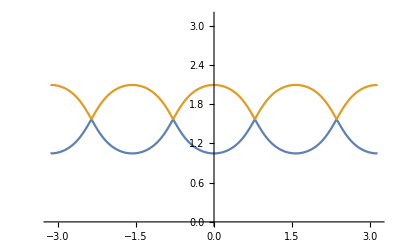
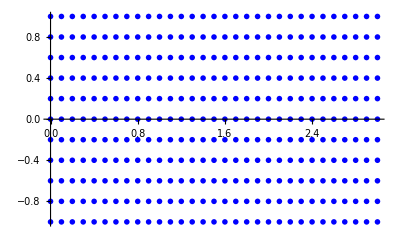
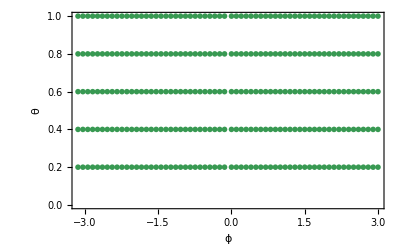
Show[-Graphics-,-Graphics-,-Graphics-,ListPlot[$Failed,PlotStyle→RGBColor[1, 0.5, 0]]]

```mathematica
gsPlot=ListPlot[originGS,PlotStyle->Orange];
confPlot=ListPlot[Transpose[{phi,theta}],Frame->{True,True,False,False},FrameLabel->{"ϕ","θ"},Axes->False,PlotRangePadding->Automatic,PlotMarkers->{marker1,0.03}];
actGSPlot=ListPlot[actualGS,PlotStyle->Blue,PlotMarkers->{"X",20}];
boundPlot=Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,-π,π},PlotRange->{{-180Degree,180Degree},{0,π}}];
Show[boundPlot,actGSPlot,confPlot,gsPlot]
```